```mathematica
(*Define Bz for several aspect ratio*)

ClearAll[R,l]
R=0.08;
l=0.3;
Bz[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));
Bz1[z_]=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz[0];

R=0.08;
l=0.16;
Bz[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));
Bz[0]
Bz2[z_]=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz[0];
R=0.08;
l=0.08;
Bz[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));
Bz[0]
Bz3[z_]=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz[0];
R=0.08;
l=0.04;
Bz[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));
Bz[0]
Bz4[z_]=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz[0];
```

1.41421

0.894427

0.485071

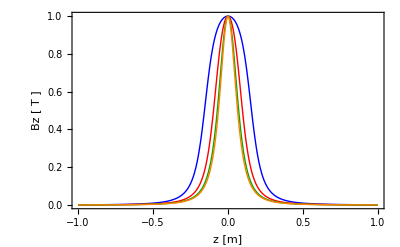

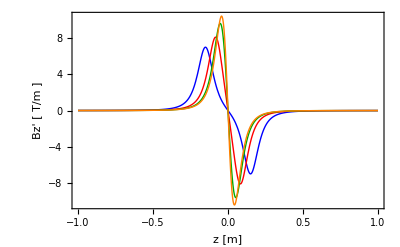

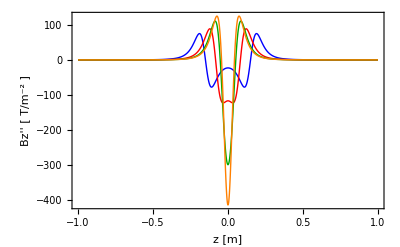

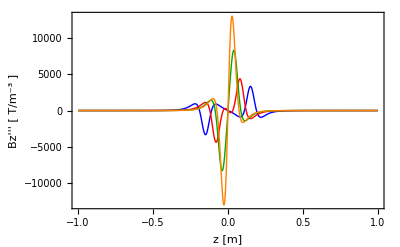

```mathematica
(*Making graphics of Bz and Derivation of Bz*)

SAR[1]=Plot[{Bz1[z],Bz2[z],Bz3[z],Bz4[z]},{z,-1,1},PlotRange->All,Frame->True,PlotStyle->{Blue,Red,Darker[Green],Orange},Axes->None,FrameLabel->{"z [m]","Bz [ T ]"},LabelStyle->Directive[15]]
SAR[2]=Plot[{Bz1'[z],Bz2'[z],Bz3'[z],Bz4'[z]},{z,-1,1},PlotRange->All,Frame->True,PlotStyle->{Blue,Red,Darker[Green],Orange},Axes->None,FrameLabel->{"z [m]","Bz' [ T/m ]"},LabelStyle->Directive[15]]

SAR[3]=Plot[{Bz1''[z],Bz2''[z],Bz3''[z],Bz4''[z]},{z,-1,1},PlotRange->All,Frame->True,PlotStyle->{Blue,Red,Darker[Green],Orange},Axes->None,FrameLabel->{"z [m]","Bz'' [ T/m^-2 ]"},LabelStyle->Directive[15]]
SAR[4]=Plot[{Bz1'''[z],Bz2'''[z],Bz3'''[z],Bz4'''[z]},{z,-1,1},PlotRange->All,Frame->True,PlotStyle->{Blue,Red,Darker[Green],Orange},Axes->None,FrameLabel->{"z [m]","Bz''' [ T/m^-3 ]"},LabelStyle->Directive[15]]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/Mag_Field_SeveralAR_d0.eps",SAR[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/Mag_Field_SeveralAR_d1.eps",SAR[2],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/Mag_Field_SeveralAR_d2.eps",SAR[3],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/Mag_Field_SeveralAR_d3.eps",SAR[4],"EPS"];
```